# Mathematica Homework I

Brian Carlson and Logan Houchens 2-5-2014

## Problem 1.

```mathematica
f[x_] = (-30*x^3 - 3*x + 7 + ⅇ^(-0.001*x))/(3*x^3 - 27 - 3 ⅇ^(.001x))
```

(7+ⅇ^(-0.001 x)-3 x-30 x^3)/(-27-3 ⅇ^(0.001 x)+3 x^3)

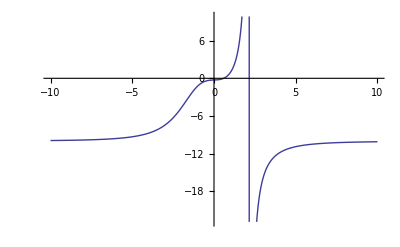

```mathematica
Tooltip[Plot[f[x],{x,-10,10}],"Look at that nice graph!"]
```

## Problem 2.

```mathematica
g[x_]=x^5-302 x^3+893 x^2+1208x-3588
```

-3588+1208 x+893 x^2-302 x^3+x^5

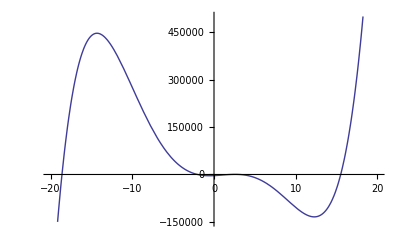

```mathematica
Plot[g[x],{x,-20,20},PlotRange->{-150000,500000}]
```

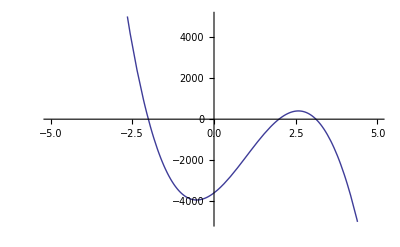

```mathematica
Plot[g[x],{x,-5,5},PlotRange->{-5000,5000}]
```

## Problem 3.

```mathematica
h[x_]= ⅇ^(2x) - 4 ⅇ^x + 2
```

2-4 ⅇ^x+ⅇ^(2 x)

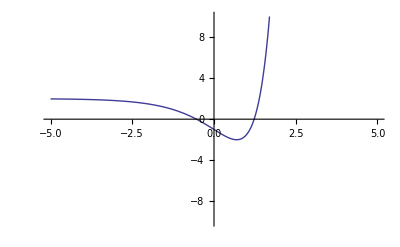

```mathematica
Plot[h[x],{x,-5,5},PlotRange->{-10,10}]
```

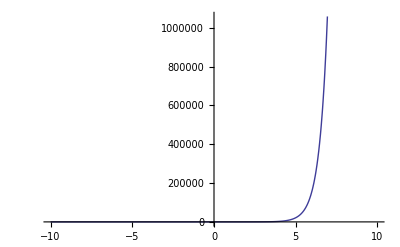

```mathematica
Plot[h[x],{x,-10,10}]
```

## Problem 4.

```mathematica
l[x_]= Log[5x + 500] + x/20
```

x/20+Log[500+5 x]

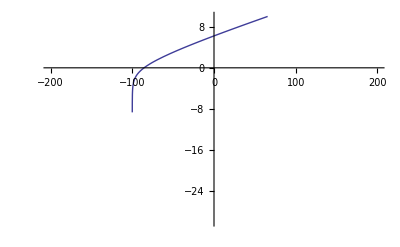

```mathematica
Plot[l[x],{x,-200,200},PlotRange->{-30,10}]
```

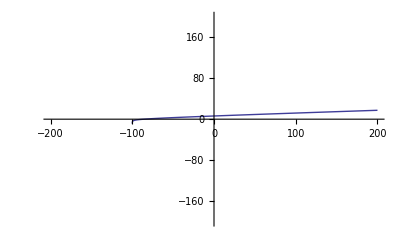

```mathematica
Plot[l[x],{x,-200,200},PlotRange->{-200,200}]
```

## Problem 5.

```mathematica
p[x_]=Cos[x/4]^2 + Sin[x/4]
```

Cos[x/4]^2+Sin[x/4]

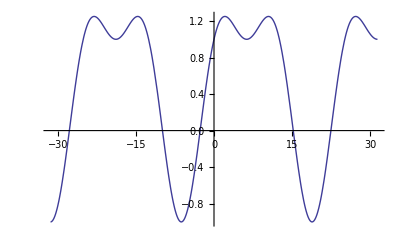

```mathematica
Plot[p[x], {x,-10π,10π}]
```

## Problem 6.

```mathematica
NSolve[0 == 4 x^3 - 3 x^2 - 3x + 7]
```

{{x→-1.16985},{x→0.959923-0.757939 ⅈ},{x→0.959923+0.757939 ⅈ}}

## Problem 7.

```mathematica
NSolve[0 == x^5 + 2 x^4 - 302 x^3 + 893 x^2 + 1208x - 3588]
```

{{x→-19.5739},{x→-2.00268},{x→1.96386},{x→3.24355},{x→14.3692}}

## Problem 8.

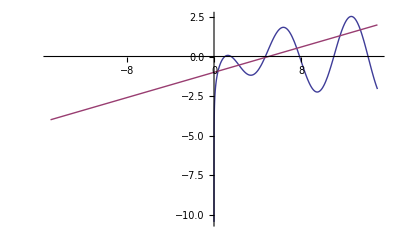

```mathematica
Plot[{Log[x]Cos[x], 2/10 x-1},{x,-15,15}]
```

```mathematica
FindRoot[Log[x]Cos[x]==(2/10 x-1),{x,.5}]
```

{x→0.370362}

```mathematica
FindRoot[Log[x]Cos[x]==(2/10 x-1),{x, 2}]
```

{x→2.28655}

```mathematica
FindRoot[Log[x]Cos[x]==(2/10 x-1),{x,5}]
```

{x→4.66948}

```mathematica
FindRoot[Log[x]Cos[x]==(2/10 x-1),{x,8}]
```

{x→7.59511}

```mathematica
FindRoot[Log[x]Cos[x]==(2/10 x-1),{x,11}]
```

{x→11.5614}

```mathematica
FindRoot[Log[x]Cos[x]==(2/10 x-1),{x,14}]
```

{x→13.4307}

## Problem 9.

```mathematica
Factor[x^6-1]
```

(-1+x) (1+x) (1-x+x^2) (1+x+x^2)

```mathematica
Factor[x^15-1]
```

(-1+x) (1+x+x^2) (1+x+x^2+x^3+x^4) (1-x+x^3-x^4+x^5-x^7+x^8)

```mathematica
Factor[x^21-1]
```

(-1+x) (1+x+x^2) (1+x+x^2+x^3+x^4+x^5+x^6) (1-x+x^3-x^4+x^6-x^8+x^9-x^11+x^12)

```mathematica
Factor[x^55-1]
```

(-1+x) (1+x+x^2+x^3+x^4) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10) (1-x+x^5-x^6+x^10-x^12+x^15-x^17+x^20-x^23+x^25-x^28+x^30-x^34+x^35-x^39+x^40)

```mathematica
Factor[x^65-1]
```

(-1+x) (1+x+x^2+x^3+x^4) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12) (1-x+x^5-x^6+x^10-x^11+x^13-x^14+x^15-x^16+x^18-x^19+x^20-x^21+x^23-x^24+x^25-x^27+x^28-x^29+x^30-x^32+x^33-x^34+x^35-x^37+x^38-x^42+x^43-x^47+x^48)

The visible pattern is that each factorization starts with (x-1) and that the highest exponents in each factor, when added together, equal the exponent in the expression we were factoring.

```mathematica
Factor[x^26-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12)

26 = 1 + 1 + 12+ 12

```mathematica
Factor[x^35-1]
```

(-1+x) (1+x+x^2+x^3+x^4) (1+x+x^2+x^3+x^4+x^5+x^6) (1-x+x^5-x^6+x^7-x^8+x^10-x^11+x^12-x^13+x^14-x^16+x^17-x^18+x^19-x^23+x^24)

35 = 1 + 4 + 6 + 24

```mathematica
Factor[x^23-1]
```

(-1+x) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12+x^13+x^14+x^15+x^16+x^17+x^18+x^19+x^20+x^21+x^22)

23 = 1 + 22

```mathematica
Factor[x^32-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8) (1+x^16)

32 = 1 + 1 + 2 + 4 + 8 + 16

## Problem 10.

```mathematica
q[n_] = x^(2^n)-1
```

-1+x^(2^n)

```mathematica
Factor[q[1]]
```

(-1+x) (1+x)

```mathematica
Factor[q[2]]
```

(-1+x) (1+x) (1+x^2)

```mathematica
Factor[q[3]]
```

(-1+x) (1+x) (1+x^2) (1+x^4)

```mathematica
Factor[q[4]]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8)

```mathematica
Factor[q[5]]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8) (1+x^16)

The pattern clearly shows that every first factor is (x-1). For every value of “n,” there is another factor added. The factors of all expressions in this format begin the same with (x-1) and (x+1) and, for every added factor, the exponent of x in the added factor increases by a factor of 2.

## Problem 11.

```mathematica
ratio = 300000/(8000*5280)
```

5/704

```mathematica
N[10 ratio]
```

0.0710227

The atmosphere would extend roughly 0.0710227 inches above the surface of the ball.

## Problem 12.

```mathematica
list= RealDigits[√2-1,10,517]
```

{{4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8,0,1,6,8,8,7,2,4,2,0,9,6,9,8,0,7,8,5,6,9,6,7,1,8,7,5,3,7,6,9,4,8,0,7,3,1,7,6,6,7,9,7,3,7,9,9,0,7,3,2,4,7,8,4,6,2,1,0,7,0,3,8,8,5,0,3,8,7,5,3,4,3,2,7,6,4,1,5,7,2,7,3,5,0,1,3,8,4,6,2,3,0,9,1,2,2,9,7,0,2,4,9,2,4,8,3,6,0,5,5,8,5,0,7,3,7,2,1,2,6,4,4,1,2,1,4,9,7,0,9,9,9,3,5,8,3,1,4,1,3,2,2,2,6,6,5,9,2,7,5,0,5,5,9,2,7,5,5,7,9,9,9,5,0,5,0,1,1,5,2,7,8,2,0,6,0,5,7,1,4,7,0,1,0,9,5,5,9,9,7,1,6,0,5,9,7,0,2,7,4,5,3,4,5,9,6,8,6,2,0,1,4,7,2,8,5,1,7,4,1,8,6,4,0,8,8,9,1,9,8,6,0,9,5,5,2,3,2,9,2,3,0,4,8,4,3,0,8,7,1,4,3,2,1,4,5,0,8,3,9,7,6,2,6,0,3,6,2,7,9,9,5,2,5,1,4,0,7,9,8,9,6,8,7,2,5,3,3,9,6,5,4,6,3,3,1,8,0,8,8,2,9,6,4,0,6,2,0,6,1,5,2,5,8,3,5,2,3,9,5,0,5,4,7,4,5,7,5,0,2,8,7,7,5,9,9,6,1,7,2,9,8,3,5,5,7,5,2,2,0,3,3,7,5,3,1,8,5,7,0,1,1,3,5,4,3,7,4,6,0,3,4,0,8,4,9,8,8,4,7,1,6,0,3,8,6,8,9,9,9,7,0,6,9,9,0,0,4,8,1,5,0,3,0,5,4,4,0,2,7,7,9,0,3,1,6,4,5,4,2,4,7,8,2,3,0,6,8,4,9,2,9,3,6,9,1,8,6,2,1,5,8,0,5,7,8,4,6,3,1,1,1,5,9,6,6,6,8,7,1,3,0,1,3,0,1,5,6,1,8,5,6,8,9,8,7,2,3,7,2,3,5,2,8,8,5,0,9,2,6,4,8,6,1,2,4,9,4},0}

```mathematica
numberList = First[list]
```

{4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8,0,1,6,8,8,7,2,4,2,0,9,6,9,8,0,7,8,5,6,9,6,7,1,8,7,5,3,7,6,9,4,8,0,7,3,1,7,6,6,7,9,7,3,7,9,9,0,7,3,2,4,7,8,4,6,2,1,0,7,0,3,8,8,5,0,3,8,7,5,3,4,3,2,7,6,4,1,5,7,2,7,3,5,0,1,3,8,4,6,2,3,0,9,1,2,2,9,7,0,2,4,9,2,4,8,3,6,0,5,5,8,5,0,7,3,7,2,1,2,6,4,4,1,2,1,4,9,7,0,9,9,9,3,5,8,3,1,4,1,3,2,2,2,6,6,5,9,2,7,5,0,5,5,9,2,7,5,5,7,9,9,9,5,0,5,0,1,1,5,2,7,8,2,0,6,0,5,7,1,4,7,0,1,0,9,5,5,9,9,7,1,6,0,5,9,7,0,2,7,4,5,3,4,5,9,6,8,6,2,0,1,4,7,2,8,5,1,7,4,1,8,6,4,0,8,8,9,1,9,8,6,0,9,5,5,2,3,2,9,2,3,0,4,8,4,3,0,8,7,1,4,3,2,1,4,5,0,8,3,9,7,6,2,6,0,3,6,2,7,9,9,5,2,5,1,4,0,7,9,8,9,6,8,7,2,5,3,3,9,6,5,4,6,3,3,1,8,0,8,8,2,9,6,4,0,6,2,0,6,1,5,2,5,8,3,5,2,3,9,5,0,5,4,7,4,5,7,5,0,2,8,7,7,5,9,9,6,1,7,2,9,8,3,5,5,7,5,2,2,0,3,3,7,5,3,1,8,5,7,0,1,1,3,5,4,3,7,4,6,0,3,4,0,8,4,9,8,8,4,7,1,6,0,3,8,6,8,9,9,9,7,0,6,9,9,0,0,4,8,1,5,0,3,0,5,4,4,0,2,7,7,9,0,3,1,6,4,5,4,2,4,7,8,2,3,0,6,8,4,9,2,9,3,6,9,1,8,6,2,1,5,8,0,5,7,8,4,6,3,1,1,1,5,9,6,6,6,8,7,1,3,0,1,3,0,1,5,6,1,8,5,6,8,9,8,7,2,3,7,2,3,5,2,8,8,5,0,9,2,6,4,8,6,1,2,4,9,4}

```mathematica
Last[numberList]
```

4

The 517th decimal digit of √2 is 4.

## Problem 13.

```mathematica
NSolve[1.00/x== 1.06/1416.5]
```

{{x→1336.32}}

Laurie’s old salary was $1336.32 per month.

## Problem 14.

```mathematica
Abs[40-4 √103]
```

-40+4 √103

The exact absolute value is 4√103- 40.

## Problem 15.

```mathematica
NSolve[x^3== -27,x]
```

{{x→-3.},{x→1.5-2.59808 ⅈ},{x→1.5+2.59808 ⅈ}}

## Problem 16.

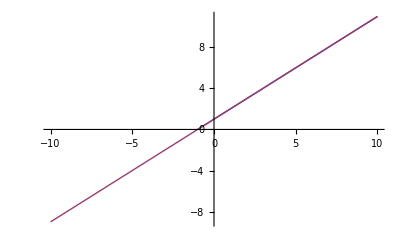

```mathematica
Plot[{((x+1)^3)^(1/3),x+1},{x,-10,10}]
```

It appears to always be true. My graphing calculator displays the same thing.

Or do they?

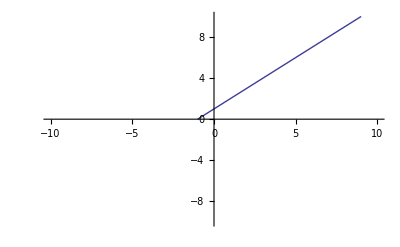

```mathematica
Plot[((x+1)^3)^(1/3),{x,-10,10},PlotRange->{-10,10}]
```

The graph goes into imaginary numbers once x+1 begins to equal a negative number. These are not equal to each other.